## Mathematica for 1D propagation

```mathematica
SetDirectory["/Users/johnhawthorne/Desktop/Vahala_Research/SixSpinorJestadt/YProp4Spin/L2=3500_standard"];
FileNames[]
```

{fort.100000,fort.100200,fort.100400,fort.100600,fort.100800,fort.101000,fort.101200,fort.101400,fort.101600,fort.101800,fort.102000,fort.102200,fort.102400,fort.102600,fort.102800,fort.103000,fort.103200,fort.103400,fort.103600,fort.103800,fort.104000,fort.104200,fort.104400,fort.104600,fort.104800,fort.105000,fort.105200,fort.105400,fort.105600,fort.105800,fort.106000,fort.106200,fort.106400,fort.106600,fort.106800,fort.107000,fort.107200,fort.107400,fort.107600,fort.107800,fort.108000,fort.108200,fort.108400,fort.108600,fort.108800,fort.109000,fort.109200,fort.109400,fort.109600,fort.109800,fort.110000,fort.200000,fort.200200,fort.200400,fort.200600,fort.200800,fort.201000,fort.201200,fort.201400,fort.201600,fort.201800,fort.202000,fort.202200,fort.202400,fort.202600,fort.202800,fort.203000,fort.203200,fort.203400,fort.203600,fort.203800,fort.204000,fort.204200,fort.204400,fort.204600,fort.204800,fort.205000,fort.205200,fort.205400,fort.205600,fort.205800,fort.206000,fort.206200,fort.206400,fort.206600,fort.206800,fort.207000,fort.207200,fort.207400,fort.207600,fort.207800,fort.208000,fort.208200,fort.208400,fort.208600,fort.208800,fort.209000,fort.209200,fort.209400,fort.209600,fort.209800,fort.210000,fort.34,fort.9}

```mathematica
(* -------- PLOTTING FORTRAN OUTPUT ---------*)

ClearAll["Global`*"];
NumFiles=50;
stepSize=200;
Do[Ez[i*stepSize]=Import[StringJoin["fort.",ToString[200000+i*stepSize]],"Table" ];
psi1[i*stepSize]=Ez[i*stepSize],
{i,0,NumFiles}];
```

```mathematica
NumFiles=50;
stepSize=200;
Do[Bx[i*stepSize]=Import[StringJoin["fort.",ToString[100000+i*stepSize]],"Table" ];
psi2[i*stepSize]=Bx[i*stepSize],
{i,0,NumFiles}];
```

### Poytning Flux - time evolution

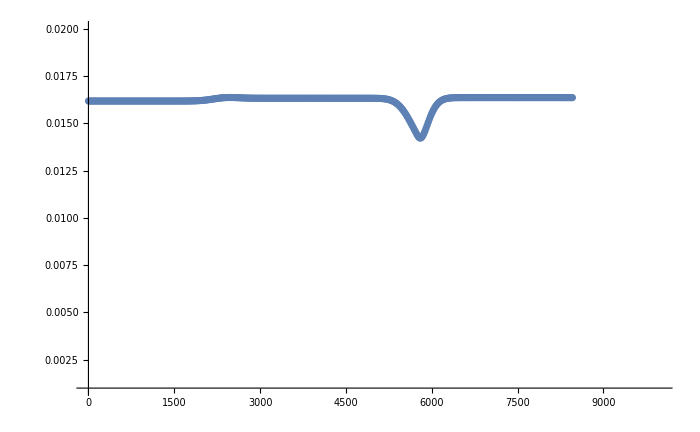

```mathematica
Poynt = Import["fort.34","Table"];ListPlot[Poynt,PlotRange->{{0,10000},{.001,.020}},ImageSize->700]
```

```mathematica
(*  for 55k < t < 110k , the pulse is straddling the region of inhomogeneous dielectric region *)
```

### Ez, Bx - profiles

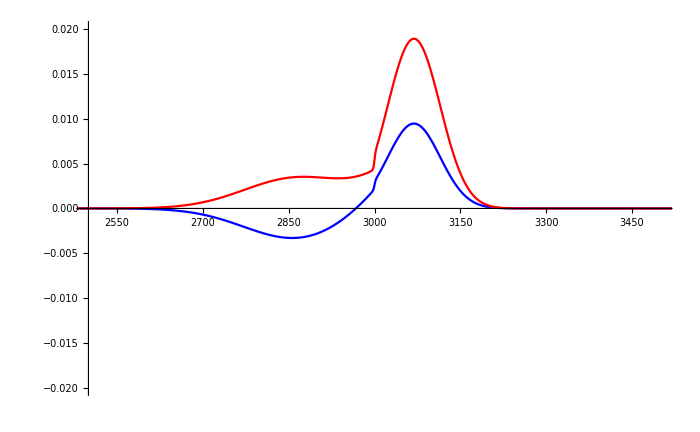

```mathematica
ListPlot[{Ez[2800],Bx[2800]},PlotRange->{{2500,3500},{-0.02,0.02}},ImageSize->700,LabelStyle->Directive[FontSize->24],PlotStyle->{Blue,Red,Black,Green},Joined->True,FrameLabel->{"x"}]
```

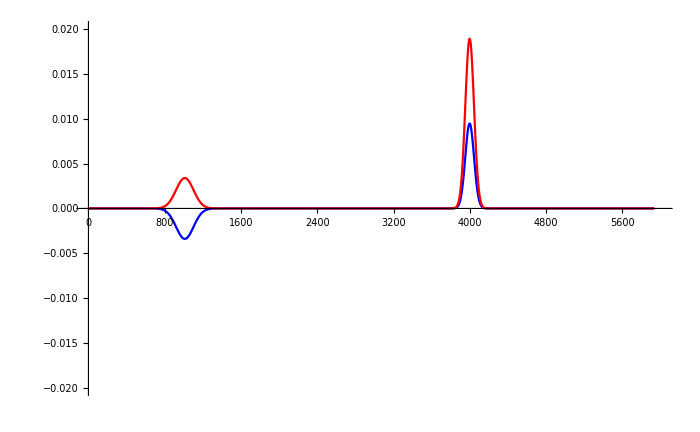

```mathematica
ListPlot[{Ez[9000],Bx[9000]},PlotRange->{{0,6000},{-0.02,0.02}},ImageSize->700,LabelStyle->Directive[FontSize->24],PlotStyle->{Blue,Red,Black,Green},Joined->True,FrameLabel->{"x"}]
```

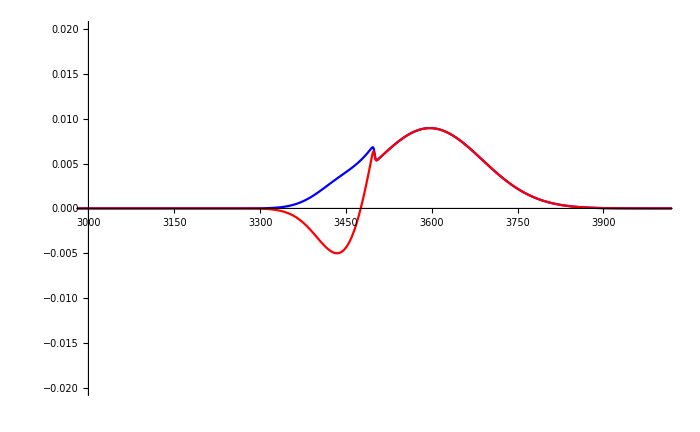

MaxValue::objfs: The objective function {0,0.000020773} should be scalar-valued.

MaxValue::ivar: 0 is not a valid variable. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/General/ivar",
ButtonNote->"MaxValue::ivar"]

```mathematica
ListPlot[{Ez[6000],Bx[6000]},PlotRange->{{3000,4000},{-0.02,0.02}},ImageSize->700,LabelStyle->Directive[FontSize->24],PlotStyle->{Blue,Red,Black,Green},Joined->True,FrameLabel->{"x"}]
```

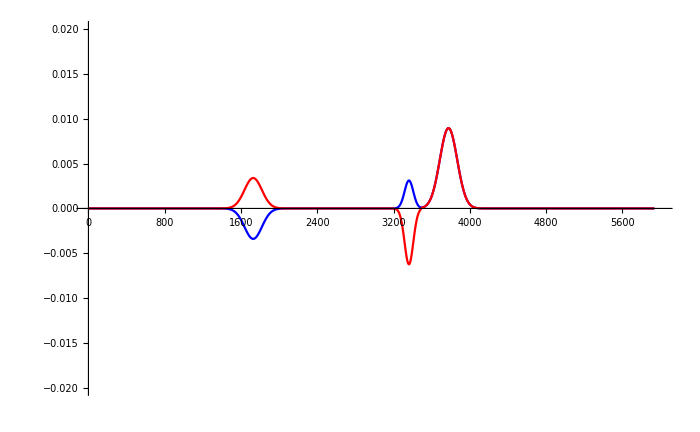

```mathematica
ListPlot[{Ez[6600],Bx[6600]},PlotRange->{{000,6000},{-0.02,0.02}},ImageSize->700,LabelStyle->Directive[FontSize->24],PlotStyle->{Blue,Red,Black,Green},Joined->True,FrameLabel->{"x"}]
```

```mathematica
ListPlot[{Ez[10800],Bx[10800]},PlotRange->{{0,2400},{-0.2751,0.2751}},ImageSize->700,LabelStyle->Directive[FontSize->24],PlotStyle->{{Blue,Dashed},Red,Black,Green},Joined->True,FrameLabel->{"x"}]
```

```mathematica
ListPlot[{Ez[116000],Bx[116000]},PlotRange->{{000,24000},{-0.21,0.21}},ImageSize->700,LabelStyle->Directive[FontSize->24],PlotStyle->{Blue,Red,Black,Green},Joined->True,FrameLabel->{"x"}]
```

```mathematica
ListPlot[{Ez[140000],Bx[140000]},PlotRange->{{0000,24000},{-0.3,0.3}},ImageSize->700,LabelStyle->Directive[FontSize->24],PlotStyle->{Blue,Red,Black,Green},Joined->True,FrameLabel->{"x"}]
```

```mathematica
ListPlot[{Ez[180000],Bx[180000]},PlotRange->{{0000,26000},{-0.21,0.21}},ImageSize->700,LabelStyle->Directive[FontSize->24],PlotStyle->{Blue,Red,Black,Green},Joined->True,FrameLabel->{"x"}]
```